Reinforcement reinforcement learning
070421 
v1
Faiz Ikramulla

```mathematica
(*setting the backgorund color of the notebook for contrast*)
SetOptions[SelectedNotebook[],Background->LightOrange];
SetOptions[SelectedNotebook[],FontColor-> Purple];
```

DeviceObject[…]

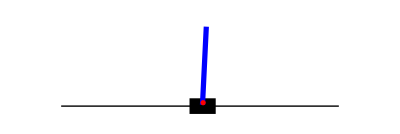

```mathematica
(*setting up the environment - cartpole here*)
env=DeviceOpen["SimulatedCartPole"]
DeviceExecute[env,"Render"]
```

```mathematica
(*setting up the policy definition - which is a chain of nets*)

policyNet=NetInitialize@NetChain[{64,Tanh,2,SoftmaxLayer[]},"Input"->4,"Output"->NetDecoder[{"Class",{Left,Right}}]]
```

NetChain[<>]

Loss Function Definition

```mathematica
(*loss function defined here - based on policy gradient*)

reinforceLoss=NetGraph[{CrossEntropyLossLayer["Index"],
ThreadingLayer[#1*#2&]},{
NetPort["DiscountedReward"]->2,
{NetPort["Input"],NetPort["Action"]}->1->2},
"Action"->NetEncoder[{"Class",{Left,Right}}]]
```

NetGraph[<>]

```mathematica
(*this is just a comment*)
```

NetGraph::noinfo: Input expression NetGraph[<>] contains insufficient information to interpret the result.

RandomNess entered

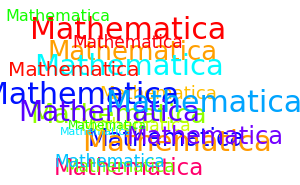

```mathematica
Graphics[Table[Text[Style["Mathematica",Hue[RandomReal[]],Italic,RandomInteger[{10,30}]],RandomReal[1,{2}],Automatic,RandomReal[{-1,1},{2}]],{20}],AspectRatio->1/GoldenRatio,ImageSize->300]
```

Training Definition

```mathematica
discountedSum[rewards_List,gamma_]:=Dot[rewards,gamma^Range[0,Length[rewards]-1]];
applyDiscount[rewards_List,gamma_]:=Table[discountedSum[Drop[rewards,i-1],gamma],{i,Length@rewards}]

CollectEpisodes[env_,policyNet_,totalNumberSteps_Integer,maxStepsPerEp_Integer,discountFactor_]:=Module[{action,actions,epActions,observedState,observedStates,epObservedStates,reward,rewards,discountedRewards,epDiscountedRewards,ended,currentSteps},epActions={};epObservedStates={};epDiscountedRewards={};
currentSteps=0;
(*episode loop*)While[currentSteps<totalNumberSteps,observedStates={};rewards={};actions={};
(*start each new episode with a fresh environment*)observedState=DeviceExecute[env,"Reset"]["ObservedState"];
(*step loop*)Do[AppendTo[observedStates,observedState];
action=policyNet[observedState];
{observedState,reward,ended}=Lookup[DeviceExecute[env,"Step",action],{"ObservedState","Reward","Ended"}];
AppendTo[rewards,reward];
AppendTo[actions,action];
If[ended,Break[]];,Min[maxStepsPerEp,totalNumberSteps-currentSteps]];
discountedRewards=applyDiscount[rewards,discountFactor];
epActions=Join[epActions,actions];
epObservedStates=Join[epObservedStates,observedStates];
epDiscountedRewards=Join[epDiscountedRewards,discountedRewards];
currentSteps+=Length@actions;];
<|"Action"->epActions,"ObservedState"->epObservedStates,"DiscountedReward"->epDiscountedRewards|>];
```

```mathematica
reinforceSampler[env_,net_,batchSize_]:=Block[{data},data=CollectEpisodes[env,net[#,"RandomSample"]&,batchSize,50,0.99];
data["Input"]=data["ObservedState"];
data];
```

```mathematica
reinforceSampler[env,policyNet,2]
```

<|Action→{Right,Right},ObservedState→{{-0.00737987,-0.0205831,0.033396,-0.0368499},{-0.00779153,0.174044,0.032659,-0.318812}},DiscountedReward→{1.99,1.},Input→{{-0.00737987,-0.0205831,0.033396,-0.0368499},{-0.00779153,0.174044,0.032659,-0.318812}}|>

TRAINING*********

```mathematica
results=NetTrain[policyNet,reinforceSampler[env,#Net,#BatchSize]&,All,LossFunction->reinforceLoss,Method->"RMSProp",BatchSize->1024,MaxTrainingRounds->50,TrainingProgressMeasurements-><|"Measurement"->NetPort["DiscountedReward"],"Aggregation"->"Mean","Key"->"Reward"|>]
trained=results["TrainedNet"];
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:50  rounds:50  time:1.6min  examples/s:549
data | ,,  training examples:1024  processed examples:51200  skipped examples:0
method | ,,  RMSPropoptimizer  batch size1024CPU
round | ,,  loss:9.39  Reward:2.16×10^1
 | 
 | ]

NOW LETS PLAY IT!!!!

```mathematica
DeviceExecute[env,"Reset"];
ListAnimate[Table[(DeviceExecute[env,"Step",DeviceExecute[env,trained[DeviceRead[env]["ObservedState"]]]];
DeviceExecute[env,"Render"]),50]];
(*not sure why it is note playing*)
```

```mathematica
(*comparisoon to RANDOM play here*)
```

```mathematica
(*DeviceExecute[env,"Reset"];
ListAnimate[Table[(DeviceExecute[env,"Step",DeviceExecute[env,"RandomAction"]];
DeviceExecute[env,"Render"]),50]];*)
```